### Start choosing the example:

```mathematica
t=21;
beta = 1;
A =0;
g[x]
```

x

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesData.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m"];Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{}|>;
d2e = Data2Equations[Data/.{I1->1,I2->2,U1->1,U2->2, U3->3}];
```

```mathematica
NonLinear[d2e];
```

```mathematica
GetKirchhoffMatrix[d2e]
```

The matrices B and K are: 
{(1
2
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | -1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | -1 | -1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0)}
The order of the variables is 
{j1,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j2,j20,j21,j22,j23,j24,j25,j26,j27,j28,j3,j30,j32,j34,j36,j38,j4,j5,j6,j7,j8,j9,jt1,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt2,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt3,jt30,jt31,jt32,jt33,jt34,jt35,jt36,jt37,jt38,jt39,jt4,jt40,jt41,jt42,jt43,jt44,jt45,jt46,jt47,jt48,jt49,jt5,jt50,jt51,jt52,jt53,jt54,jt55,jt56,jt57,jt58,jt59,jt6,jt60,jt61,jt62,jt63,jt64,jt7,jt8,jt9}

{SparseArray[…],SparseArray[…],{j1,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j2,j20,j21,j22,j23,j24,j25,j26,j27,j28,j3,j30,j32,j34,j36,j38,j4,j5,j6,j7,j8,j9,jt1,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt2,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt3,jt30,jt31,jt32,jt33,jt34,jt35,jt36,jt37,jt38,jt39,jt4,jt40,jt41,jt42,jt43,jt44,jt45,jt46,jt47,jt48,jt49,jt5,jt50,jt51,jt52,jt53,jt54,jt55,jt56,jt57,jt58,jt59,jt6,jt60,jt61,jt62,jt63,jt64,jt7,jt8,jt9}}

```mathematica
CriticalCongestionSolver[d2e = Data2Equations[Data/.{I1->1,I2->2,U1->1,U2->2, U3->3}]]//AbsoluteTiming
```

tripleclean done!

Preprocessing done!

{2.17189,<|j36→1,j38→2,j35→0,j37→0,j29→0,j31→0,j33→0,j2→1,j4→2,j1→0,j6→0,j8→18/13,j3→0,j5→5/13,j10→21/13,j7→0,j12→0,j14→20/13,j9→0,j11→2/13,j16→19/13,j13→0,j18→0,j20→0,j22→49/26,j15→0,j17→3/13,j24→3/26,j26→29/26,j19→3/26,j23→0,j28→0,j21→0,j30→49/26,j25→0,j32→29/26,j27→0,j34→0,u30→1,u32→2,u34→3,jt12→21/13,jt13→0,jt14→0,jt2→1,jt20→2/13,jt23→2/13,jt24→19/13,jt25→0,jt26→0,jt3→0,jt38→0,jt4→2,jt40→0,jt46→0,jt5→0,jt50→0,jt51→0,jt52→0,jt53→0,jt54→0,jt55→3/26,jt56→0,jt58→0,jt59→49/26,jt6→1,jt60→0,jt61→29/26,jt62→0,jt63→0,jt64→0,jt7→0,jt8→5/13,jt9→0,u29→1,u31→2,u33→3,u36→177/26,u38→213/26,jt1→0,jt35→0,jt39→0,jt43→29/26,jt57→0,u10→119/26,u13→115/26,u14→75/26,u15→119/26,u16→81/26,u17→75/26,u18→81/26,u2→151/26,u20→3,u21→75/26,u22→1,u25→81/26,u26→2,u27→3,u28→3,u35→177/26,u37→213/26,u4→161/26,u7→151/26,u8→115/26,u9→161/26,jt15→0,jt21→0,jt18→18/13,jt31→20/13,jt36→0,jt37→3/26,jt49→0,u1→177/26,u11→115/26,u12→119/26,u19→75/26,u23→81/26,u24→3,u3→213/26,u5→151/26,u6→161/26,jt48→0,jt10→0,jt11→5/13,jt16→0,jt17→0,jt19→0,jt22→0,jt27→0,jt28→0,jt29→0,jt30→0,jt32→0,jt33→0,jt34→3/13,jt41→3/13,jt42→3/26,jt44→0,jt45→0,jt47→0|>}

```mathematica
Module[{bb},
f=Association["f"->Function[x,x^2]]["f"];
f[4]
]
```

16

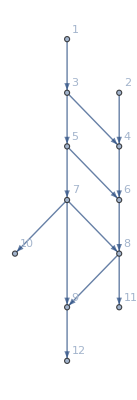

```mathematica
AdjacencyGraph[Data["Vertices List"],Data["Adjacency Matrix"],VertexLabels->"Name"]
```

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.77;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],4,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],9,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

# kdkd

```mathematica
(*Wolfram Language package*)D2E::usage="D2E[<|\"Vertices List\" -> {1, 2, 3}, \"Adjacency Matrix\" -> {{0, 0, 0}, {1, 0, 1}, {0, 0, 0}}, 
 \"Entrance Vertices and Currents\" -> {{2, I1}}, 
 \"Exit Vertices and Terminal Costs\" -> {{1, U1}, {3, U2}}, 
 \"Switching Costs\" -> {{1, 2, 3, S1}, {3, 2, 1, S2}}|> returns the equations for the stationary mean-field game on the network.]"

Begin["`Private`"]
D2E[Data_Association]:=Module[{BG,FG,AuxiliaryGraph,VL,FVL,EntranceVertices,InwardVertices,ExitVertices,OutwardVertices,EL,BEL,OutEdges,InEdges,ExitNeighbors,AllTransitions,EqCcs,SC=Lookup[Data,"Switching Costs",{}],jargs,js,jvars,jts,jtvars,uargs,us,uvars,SignedCurrents,EntryArgs,NoDeadEnds,NoDeadStarts,ExitCosts,EntryDataAssociation,SwitchingCosts,EqPosCon,EqCurrentCompCon,EqTransitionCompCon,EqSwitchingByVertex,EqSwitchingConditions,EqCompCon,EqValueAuxiliaryEdges,EqBalanceSplittingCurrents,EqBalanceGatheringCurrents,Nrhs,Nlhs,MinimalTimeRhs,AllOr,EqAllAll,AllIneq,EqCriticalCase,EqMinimalTime,EqNonCritical,EqPosJs,TrueEq,costpluscurrents,RuleBalanceGatheringCurrents,RuleEntryIn,RuleEntryOut,RuleExitValues,RuleExitCurrentsIn,InitRules,OutRules,InRules,RuleNonCritical,RuleNonCritical1,RulesCriticalCase,RulesCriticalCase1,(*,EqNonCritical1*)EqPosJts,BalanceSplittingCurrents,BalanceGatheringCurrents,EqEntryIn,Kirchhoff,RuleValueAuxiliaryEdges,BM,KM,vars},(*Checking consistency on the swithing costs*)If[SC=!={},ConsistentSwithingCosts[sc_][{a_,b_,c_,S_}]:=Module[{or,de,bounds},or=Cases[sc,{a,b,_,_}];
de=Cases[sc,{_,b,c,_}];
bounds=Outer[Plus,Last/@or,Last/@de]//Flatten;
(*And@@(NonNegative[#-S]&)/@bounds*)And@@(#>=S&)/@bounds];
EqCcs=ConsistentSwithingCosts[SC]/@SC;
EqCcs=Simplify[EqCcs];
If[AnyTrue[EqCcs,#===False&],Print["DataToEquations: Triangle inequalities for switching costs: \n",Select[AssociationThread[SC,EqCcs],Function[exp,!TrueQ[exp]]]];
Print["DataToEquations: The switching costs are ",Style["incompatible",Red],". \nStopping!"];
Return[]]];
(****Graph stuff****)BG=AdjacencyGraph[Data["Vertices List"],Data["Adjacency Matrix"],VertexLabels->"Name",DirectedEdges->True];
EntranceVertices=First/@Data["Entrance Vertices and Currents"];
ExitVertices=First/@Data["Exit Vertices and Terminal Costs"];
Clear["en*"];
(*InwardVertices defines auxiliary vertices for the entrance vertices*)InwardVertices=AssociationThread[EntranceVertices,Symbol["en"<>ToString[#]]&/@EntranceVertices];
Clear["ex*"];
OutwardVertices=AssociationThread[ExitVertices,Symbol["ex"<>ToString[#]]&/@ExitVertices];
(*InEdges defines auxiliary arguments for the entrance vertices*)InEdges=MapThread[DirectedEdge,{InwardVertices/@EntranceVertices,EntranceVertices}];
OutEdges=MapThread[DirectedEdge,{ExitVertices,OutwardVertices/@ExitVertices}];
AuxiliaryGraph=Graph[Join[InEdges,OutEdges],VertexLabels->"Name",GraphLayout->"SpringEmbedding"];
FG=EdgeAdd[BG,Join[InEdges,OutEdges]];
VL=Data["Vertices List"];
EL=EdgeList[FG];
BEL=EdgeList[BG];
FVL=VertexList[FG];
(*arguments*)jargs=Flatten[#,1]&@({AtTail@#,AtHead@#}&/@EL);
uargs=jargs;
AllTransitions=TransitionsAt[FG,#]&/@FVL//Catenate(*at vertex from first edge to second edge*);
EntryArgs=AtHead/@((EdgeList[AuxiliaryGraph,_->#]&/@(First/@Data["Entrance Vertices and Currents"]))//Flatten[#,1]&);
EntryDataAssociation=RoundValues@AssociationThread[EntryArgs,Last/@Data["Entrance Vertices and Currents"]];
ExitCosts=AssociationThread[OutwardVertices/@(First/@Data["Exit Vertices and Terminal Costs"]),Last/@Data["Exit Vertices and Terminal Costs"]];
(*variables*)js=Table[Symbol["j"<>ToString[k]],{k,1,Length@jargs}];
jvars=AssociationThread[jargs,js];
jts=Table[Symbol["jt"<>ToString[k]],{k,1,Length@AllTransitions}];
jtvars=AssociationThread[AllTransitions,jts];
us=Table[Symbol["u"<>ToString[k]],{k,1,Length@uargs}];
uvars=AssociationThread[uargs,us];
costpluscurrents=Table[Symbol["cpc"<>ToString[k]],{k,1,Length@BEL}];
(*costpluscurrentsvars=AssociationThread[BEL,costpluscurrents];*)SignedCurrents=AssociationThread[BEL,(jvars[AtHead[#]]-jvars[AtTail[#]]&)/@BEL];
Print["D2E: Variables are all set"];
(*Elements of the system*)(*Swithing cost is initialized with 0. AssociationThread associates the last association!*)SwitchingCosts=AssociationThread[Join[AllTransitions,triple2path[Take[#,3],FG]&/@SC],Join[0&/@AllTransitions,Last[#]&/@SC]];
SC=path2triple/@Normal[SwitchingCosts];
If[SC=!={},Print["Second check:"];
(*ConsistentSwithingCosts[{a_,b_,c_,S_}]:=Module[{sc=SC,or,de,bounds},or=Cases[sc,{a,b,_,_}];
de=Cases[sc,{_,b,c,_}];
bounds=Outer[Plus,Last/@or,Last/@de]//Flatten;
(*And@@(NonNegative[#-S]&)/@bounds*)And@@(#>=S&)/@bounds];*)EqCcs=ConsistentSwithingCosts[SC]/@SC;
EqCcs=Simplify[EqCcs];
(*Print[EqCcs];*)If[AnyTrue[EqCcs,#===False&],Print["DataToEquations: Triangle inequalities for switching costs: ",Select[AssociationThread[SC,EqCcs],Function[exp,!TrueQ[exp]]]];
Print["DataToEquations: The switching costs are ",Style["incompatible",Red],". \nStopping!"];
Return[]]];
EqPosJs=And@@(#>=0&/@Join[jvars]);(*Inequality*)EqPosJts=And@@(#>=0&/@Join[jtvars]);(*Inequality*)EqPosCon=EqPosJs&&EqPosJts;(*Inequality*)EqCurrentCompCon=And@@(CurrentCompCon[jvars]/@EL);(*Or*)EqTransitionCompCon=And@@((Sort/@TransitionCompCon[jtvars]/@AllTransitions)//Union);(*Or*)(*Balance Splitting Currents in the full graph*)NoDeadEnds=IncomingEdges[FG]/@VL//Flatten[#,1]&;
EqBalanceSplittingCurrents=And@@((jvars[#]==Total[jtvars/@CurrentSplitting[AllTransitions][#]])&/@NoDeadEnds);(*Equal*)BalanceSplittingCurrents=((jvars[#]-Total[jtvars/@CurrentSplitting[AllTransitions][#]])&/@NoDeadEnds);
(*Gathering currents in the inside of the basic graph*)NoDeadStarts=OutgoingEdges[FG]/@VL//Flatten[#,1]&;
RuleBalanceGatheringCurrents=(jvars[#]->Total[jtvars/@CurrentGathering[AllTransitions][#]])&/@NoDeadStarts;(*Rule*)(*First rules:these have some j in terms of jts*)InitRules=Association[RuleBalanceGatheringCurrents];
(*get equations for the exit currents at the entry vertices*)BalanceGatheringCurrents=((-jvars[#]+Total[jtvars/@CurrentGathering[AllTransitions][#]])&/@NoDeadStarts);
EqBalanceGatheringCurrents=Simplify/@(And@@(#==0&/@BalanceGatheringCurrents));
(*Incoming currents*)EqEntryIn=(jvars[#]==EntryDataAssociation[#])&/@(AtHead/@InEdges);(*List of Equals*)RuleEntryIn=Flatten[ToRules/@EqEntryIn];(*List of Rules*)Kirchhoff=Join[EqEntryIn,(#==0&/@(BalanceGatheringCurrents+BalanceSplittingCurrents))];
(*Print["The matrices B and K are: \n",MatrixForm/@CoefficientArrays[Kirchhoff,vars=RandomSample@Join[js,jts]],"\nThe order of the variables is \n",vars];*)(*Outgoing currents at entrances*)RuleEntryOut=(jvars[#]->0)&/@(AtTail/@InEdges);(*Rule*)RuleEntryIn=Join[RuleEntryIn,RuleEntryOut];
(*Not necessary to replace RuleEntryIn in InitRules*)AssociateTo[InitRules,RuleEntryIn];
(*Include Gathering currents information in the rules*){TrueEq,InitRules}=CleanEqualities[{EqBalanceGatheringCurrents/. RuleBalanceGatheringCurrents,InitRules}];
ExitNeighbors=IncidenceList[AuxiliaryGraph,OutwardVertices/@ExitVertices];
Print[ExitNeighbors];
Print[OutEdges];
(*TODO this seems to be defined already:OutEdges*)(*Incoming currents at the exits are zero*)RuleExitCurrentsIn=ExitCurrents[jvars]/@ExitNeighbors;(*Rule*)Kirchhoff=Kirchhoff/. Join[RuleExitCurrentsIn,RuleEntryOut];
{BM,KM}=CoefficientArrays[Kirchhoff,vars=Variables[Kirchhoff/. Equal->Plus]];
Print["The matrices B and K are: \n",MatrixForm/@{-BM,KM},"\nThe order of the variables is \n",vars];
AssociateTo[InitRules,RuleExitCurrentsIn];
(*Exit values at exit vertices*)RuleExitValues=ExitRules[uvars,ExitCosts]/@ExitNeighbors;(*Rule*)(*Not necessary to replace RuleExitValues in InitRules,there are no us up to now.*)Print[RuleExitValues];
AssociateTo[InitRules,RuleExitValues];
(*The value function on the auxiliary edges is constant and equal to the exit cost.*)EqValueAuxiliaryEdges=And@@((uvars[AtHead[#]]==uvars[AtTail[#]])&/@Join[InEdges,OutEdges]);(*Equal*)RuleValueAuxiliaryEdges=(uvars[AtTail[#]]->uvars[AtHead[#]])&/@Join[InEdges,OutEdges];(*Equal*)Print["D2E: CleanEqualities for the values at the auxiliary edges"];
{TrueEq,InitRules}=CleanEqualities[{EqValueAuxiliaryEdges,InitRules}];
(*Print[RuleValueAuxiliaryEdges];*)(*Infinite switching costs here prevent the network from sucking agents from the exits.*)OutRules=Rule[#,Infinity]&/@(Outer[Flatten[{AtTail[#1],#2}]&,OutEdges,EL]//Flatten[#,1]&);
InRules=Rule[#,Infinity]&/@(Outer[{#2[[2]],#1,#2}&,IncidenceList[FG,#]&/@EntranceVertices,InEdges]//Flatten[#,2]&);
AssociateTo[SwitchingCosts,Association[OutRules]];
AssociateTo[SwitchingCosts,Association[InRules]];
Print["D2E: Assembled most elements of the system"];
(*Switching condition equations*)EqSwitchingByVertex=Transu[uvars,SwitchingCosts]/@TransitionsAt[FG,#]&/@VL;
(*EqSwitchingByVertex=BooleanConvert[Reduce[Reduce@#,Reals],"CNF"]&/@EqSwitchingByVertex;*)(*Maybe this is good with nonzeroswitching costs.*)EqSwitchingByVertex=BooleanConvert[Reduce[#,Reals],"CNF"]&/@EqSwitchingByVertex;
EqSwitchingByVertex=DeleteCases[EqSwitchingByVertex,True];
Print["D2E: CleanEqualities for the switching conditions on each vertex: \n",Reduce@EqSwitchingByVertex];
{EqSwitchingConditions,InitRules}=CleanEqualities[{EqSwitchingByVertex,InitRules}];
EqCompCon=And@@Compu[jtvars,uvars,SwitchingCosts]/@AllTransitions;(*Or*)Print["D2E: CleanEqualities for the complementary conditions (given the rules)"];
{EqCompCon,InitRules}=CleanEqualities[{EqCompCon,InitRules}];
(*Default in a,function,corresponds to the classic critical congestion case*)a (*[SignedCurrents[edge],edge]:*)=Lookup[Data,"a",Function[{j,edge},j]];
MinimalTimeRhs=Flatten[-a[SignedCurrents[#],#]+SignedCurrents[#]&/@BEL];
Nlhs=Flatten[uvars[AtHead[#]]-uvars[AtTail[#]]+SignedCurrents[#]&/@BEL];
EqMinimalTime=And@@(MapThread[(#1==#2)&,{Nlhs,MinimalTimeRhs}]);
Nrhs=Flatten[-Cost[SignedCurrents[#],#]+SignedCurrents[#]&/@BEL];(*one possible cost is IntM*)Print["D2E: CleanEqualities for the balance conditions in terms of (mostly) transition currents"];
{TrueEq,InitRules}=CleanEqualities[{EqBalanceSplittingCurrents,InitRules}];
AllOr=EqCurrentCompCon&&EqTransitionCompCon&&EqCompCon;
AllOr=AllOr/.InitRules;
AllOr=BooleanConvert[Simplify/@AllOr,"CNF"];
{AllOr,InitRules}=CleanEqualities[{AllOr,InitRules}];
EqPosCon=EqPosCon/. InitRules;
EqSwitchingConditions=EqSwitchingConditions/.InitRules;
EqSwitchingConditions=Simplify[EqSwitchingConditions];
AllOr=AllOr&&Select[EqSwitchingConditions,Head[#]===Or&];
AllOr=BooleanConvert[AllOr,"CNF"];
AllIneq=EqPosCon&&Select[EqSwitchingConditions,Head[#]=!=Or&];
AllIneq=Simplify[AllIneq];
(*AllOr=BooleanConvert[Simplify[#,AllIneq]&/@AllOr,"CNF"];
{EqAllAll,InitRules}=CleanEqualities[{AllOr&&AllIneq,InitRules}];*)EqCriticalCase=And@@((#==0)&/@Nlhs);(*Equal*)EqNonCritical=And@@(MapThread[Equal[#1,#2]&,{Nlhs,costpluscurrents/.InitRules}])/.AssociationThread[us,us/.InitRules];
RuleNonCritical1=Solve[EqNonCritical,Reals]//Quiet;
(*The operations below are commutative! Print[RuleNonCritical1/. AssociationThread[costpluscurrents,0&/@costpluscurrents]];
Print[Solve[EqNonCritical/. AssociationThread[costpluscurrents,0&/@costpluscurrents],Reals]//Quiet];*)(*Print[EqCriticalCase/.AssociationThread[us,us/.InitRules]];
Print[EqNonCritical/. AssociationThread[costpluscurrents,0&/@costpluscurrents]];
Print["right?\n",(EqCriticalCase/.AssociationThread[us,us/.InitRules])/.RuleNonCritical1];
Print["right?\n",(EqCriticalCase/. AssociationThread[costpluscurrents,0&/@costpluscurrents])/.(RuleNonCritical1/. AssociationThread[costpluscurrents,0&/@costpluscurrents])];
Print[EqNonCritical/. RuleNonCritical1];*)Print["D2E: CleanEqualities for the (non) critical case equations"];
{TrueEq,RuleNonCritical}=CleanEqualities[{EqNonCritical,InitRules}];
(*Print[Expand/@RuleNonCritical];*)EqCriticalCase=EqNonCritical/. AssociationThread[costpluscurrents,0&/@costpluscurrents];
(*Print[EqCriticalCase];*)RulesCriticalCase1=Expand/@(RuleNonCritical1/. AssociationThread[costpluscurrents,0&/@costpluscurrents]);
RulesCriticalCase=Expand/@(RuleNonCritical/. AssociationThread[costpluscurrents,0&/@costpluscurrents]);
(*Here we change the pourpose of costpluscurrents*)costpluscurrents=AssociationThread[costpluscurrents,Nrhs];
(*Print[Solve[EqCriticalCase,js]];
(*RulesCriticalCaseJs=Association@First[Solve[EqCriticalCase/.RuleEntryIn,js]];*)Print["CleanEqualities for the critical case equations"];
{TrueEq,RulesCriticalCase}=CleanEqualities[{EqCriticalCase,InitRules}];
Print["Expanding critical rules..."];
RulesCriticalCase=Expand/@RulesCriticalCase;
Print[RulesCriticalCase];*)Print["D2E: D2E is finished!"];
Print[$Context];
Print[Names[$Context<>"*"]];
ttt=1;
Print[Names[$Context<>"*"]];
Join[Data,Association[(*Graph structure*)"BG"->BG,"InEdges"->InEdges,"OutEdges"->OutEdges,"FG"->FG,(*variables*)"jvars"->jvars,"jtvars"->jtvars,"uvars"->uvars,"costpluscurrents"->costpluscurrents,"jays"->SignedCurrents,(*equations*)(*complementarity*)"AllOr"->AllOr,(*union of all complementarity conditions*)"AllIneq"->AllIneq,"EqPosJs"->EqPosJs,"EqPosJts"->EqPosJts,"EqPosCon"->EqPosCon,"EqCurrentCompCon"->EqCurrentCompCon,"EqTransitionCompCon"->EqTransitionCompCon,(*linear equations (and inequalities)*)"EqAllAll"->EqAllAll,"BoundaryRules"->InitRules,"InitRules"->InitRules,"RulesCriticalCase"->RulesCriticalCase,"RulesCriticalCase1"->RulesCriticalCase1,(*"RulesCriticalCaseJs"->RulesCriticalCaseJs,*)"RuleExitValues"->RuleExitValues,"RuleEntryIn"->RuleEntryIn,"Nlhs"->Nlhs,"MinimalTimeRhs"->MinimalTimeRhs,"EqCriticalCase"->EqCriticalCase,"EqNonCritical"->EqNonCritical,(*"EqNonCritical1"->EqNonCritical1,*)"RuleNonCritical"->RuleNonCritical,"RuleNonCritical1"->RuleNonCritical1,"EqSwitchingConditions"->And@@EqSwitchingByVertex,"EqValueAuxiliaryEdges"->EqValueAuxiliaryEdges,"EqBalanceSplittingCurrents"->EqBalanceSplittingCurrents,"EqBalanceGatheringCurrents"->EqBalanceGatheringCurrents,"Nrhs"->Nrhs,"B"->BM,"K"->KM,"NoDeadEnds"->NoDeadEnds,"NoDeadStarts"->NoDeadStarts,"EqEntryIn"->EqEntryIn,"vars"->vars]]]


(*"EntranceVertices"->EntranceVertices,*)
(*"InwardVertices"->InwardVertices,*)
(*"ExitVertices"->ExitVertices,*)
(*"OutwardVertices"->OutwardVertices,*)
(*"AuxiliaryGraph"->AuxiliaryGraph,*)
(*"VL"->VL,"EL"->EL,"BEL"->BEL,"FVL"->FVL,*)
(*"AllTransitions"->AllTransitions,"NoDeadEnds"->NoDeadEnds,"NoDeadStarts"->NoDeadStarts,*)
(*"jargs"->jargs,"js"->js,*)
(*"jts"->jts,*)
(*"uargs"->uargs,"us"->us,*)
(*"SwitchingCosts"->SwitchingCosts,*)
(*"OutRules"->OutRules,*)
(*"InRules"->InRules,*)
(*"EntryArgs"->EntryArgs,*)
(*"EntryDataAssociation"->EntryDataAssociation,*)
(*"ExitCosts"->ExitCosts,*)
(*"EqCompCon"->EqCompCon,*)
(*"EqPosCon"->EqPosCon,"EqEntryIn"->EqEntryIn,"EqExitValues"->EqExitValues,"EqValueAuxiliaryEdges"->EqValueAuxiliaryEdges,"AllIneq"->AllIneq,*)



End[]
```

# outro

```mathematica
Sign[#]*Abs[#]&[x]
```

Abs[x] Sign[x]

```mathematica
FullSimplify[Abs[x] Sign[x]]
```

x

```mathematica
KeyTake
```

```mathematica
Select[<|{1,1->3}->j1,{3,1->3}->j2,{2,2->4}->j3,{4,2->4}->j4,{3,3->4}->j5,{4,3->4}->j6,{3,3->5}->j7,{5,3->5}->j8,{4,4->6}->j9,{6,4->6}->j10,{5,5->6}->j11,{6,5->6}->j12,{5,5->7}->j13,{7,5->7}->j14,{6,6->8}->j15,{8,6->8}->j16,{7,7->8}->j17,{8,7->8}->j18,{7,7->9}->j19,{9,7->9}->j20,{7,7->10}->j21,{10,7->10}->j22,{8,8->9}->j23,{9,8->9}->j24,{8,8->11}->j25,{11,8->11}->j26,{9,9->12}->j27,{12,9->12}->j28,{10,10->ex10}->j29,{ex10,10->ex10}->j30,{11,11->ex11}->j31,{ex11,11->ex11}->j32,{12,12->ex12}->j33,{ex12,12->ex12}->j34,{en1,en1->1}->j35,{1,en1->1}->j36,{en2,en2->2}->j37,{2,en2->2}->j38|>, MemberQ[{j1,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j2,j20,j21,j22,j23,j24,j25,j26,j27,j28,j3,j30,j32,j34,j36,j38,j4,j5,j6,j7,j8,j9,jt1,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt2,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt3,jt30,jt31,jt32,jt33,jt34,jt35,jt36,jt37,jt38,jt39,jt4,jt40,jt41,jt42,jt43,jt44,jt45,jt46,jt47,jt48,jt49,jt5,jt50,jt51,jt52,jt53,jt54,jt55,jt56,jt57,jt58,jt59,jt6,jt60,jt61,jt62,jt63,jt64,jt7,jt8,jt9},#]&]
```

<|{1,1->3}→j1,{3,1->3}→j2,{2,2->4}→j3,{4,2->4}→j4,{3,3->4}→j5,{4,3->4}→j6,{3,3->5}→j7,{5,3->5}→j8,{4,4->6}→j9,{6,4->6}→j10,{5,5->6}→j11,{6,5->6}→j12,{5,5->7}→j13,{7,5->7}→j14,{6,6->8}→j15,{8,6->8}→j16,{7,7->8}→j17,{8,7->8}→j18,{7,7->9}→j19,{9,7->9}→j20,{7,7->10}→j21,{10,7->10}→j22,{8,8->9}→j23,{9,8->9}→j24,{8,8->11}→j25,{11,8->11}→j26,{9,9->12}→j27,{12,9->12}→j28,{ex10,10->ex10}→j30,{ex11,11->ex11}→j32,{ex12,12->ex12}→j34,{1,en1->1}→j36,{2,en2->2}→j38|>

```mathematica
jvars = <|{1,1->3}->j1,{3,1->3}->j2,{2,2->4}->j3,{4,2->4}->j4,{3,3->4}->j5,{4,3->4}->j6,{3,3->5}->j7,{5,3->5}->j8,{4,4->6}->j9,{6,4->6}->j10,{5,5->6}->j11,{6,5->6}->j12,{5,5->7}->j13,{7,5->7}->j14,{6,6->8}->j15,{8,6->8}->j16,{7,7->8}->j17,{8,7->8}->j18,{7,7->9}->j19,{9,7->9}->j20,{7,7->10}->j21,{10,7->10}->j22,{8,8->9}->j23,{9,8->9}->j24,{8,8->11}->j25,{11,8->11}->j26,{9,9->12}->j27,{12,9->12}->j28,{10,10->ex10}->j29,{ex10,10->ex10}->j30,{11,11->ex11}->j31,{ex11,11->ex11}->j32,{12,12->ex12}->j33,{ex12,12->ex12}->j34,{en1,en1->1}->j35,{1,en1->1}->j36,{en2,en2->2}->j37,{2,en2->2}->j38|>;
```

```mathematica
vars ={j1,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j2,j20,j21,j22,j23,j24,j25,j26,j27,j28,j3,j30,j32,j34,j36,j38,j4,j5,j6,j7,j8,j9,jt1,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt2,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt3,jt30,jt31,jt32,jt33,jt34,jt35,jt36,jt37,jt38,jt39,jt4,jt40,jt41,jt42,jt43,jt44,jt45,jt46,jt47,jt48,jt49,jt5,jt50,jt51,jt52,jt53,jt54,jt55,jt56,jt57,jt58,jt59,jt6,jt60,jt61,jt62,jt63,jt64,jt7,jt8,jt9};
```

```mathematica
Keys@Select[Join[jvars,jtvars], MemberQ[vars,#]&]
```

{{1,1->3},{3,1->3},{2,2->4},{4,2->4},{3,3->4},{4,3->4},{3,3->5},{5,3->5},{4,4->6},{6,4->6},{5,5->6},{6,5->6},{5,5->7},{7,5->7},{6,6->8},{8,6->8},{7,7->8},{8,7->8},{7,7->9},{9,7->9},{7,7->10},{10,7->10},{8,8->9},{9,8->9},{8,8->11},{11,8->11},{9,9->12},{12,9->12},{ex10,10->ex10},{ex11,11->ex11},{ex12,12->ex12},{1,en1->1},{2,en2->2},{1,1->3,en1->1},{1,en1->1,1->3},{2,2->4,en2->2},{2,en2->2,2->4},{3,1->3,3->4},{3,1->3,3->5},{3,3->4,1->3},{3,3->4,3->5},{3,3->5,1->3},{3,3->5,3->4},{4,2->4,3->4},{4,2->4,4->6},{4,3->4,2->4},{4,3->4,4->6},{4,4->6,2->4},{4,4->6,3->4},{5,3->5,5->6},{5,3->5,5->7},{5,5->6,3->5},{5,5->6,5->7},{5,5->7,3->5},{5,5->7,5->6},{6,4->6,5->6},{6,4->6,6->8},{6,5->6,4->6},{6,5->6,6->8},{6,6->8,4->6},{6,6->8,5->6},{7,5->7,7->8},{7,5->7,7->9},{7,5->7,7->10},{7,7->8,5->7},{7,7->8,7->9},{7,7->8,7->10},{7,7->9,5->7},{7,7->9,7->8},{7,7->9,7->10},{7,7->10,5->7},{7,7->10,7->8},{7,7->10,7->9},{8,6->8,7->8},{8,6->8,8->9},{8,6->8,8->11},{8,7->8,6->8},{8,7->8,8->9},{8,7->8,8->11},{8,8->9,6->8},{8,8->9,7->8},{8,8->9,8->11},{8,8->11,6->8},{8,8->11,7->8},{8,8->11,8->9},{9,7->9,8->9},{9,7->9,9->12},{9,8->9,7->9},{9,8->9,9->12},{9,9->12,7->9},{9,9->12,8->9},{10,7->10,10->ex10},{10,10->ex10,7->10},{11,8->11,11->ex11},{11,11->ex11,8->11},{12,9->12,12->ex12},{12,12->ex12,9->12}}

```mathematica
jtvars=<|{1,1->3,en1->1}->jt1,{1,en1->1,1->3}->jt2,{2,2->4,en2->2}->jt3,{2,en2->2,2->4}->jt4,{3,1->3,3->4}->jt5,{3,1->3,3->5}->jt6,{3,3->4,1->3}->jt7,{3,3->4,3->5}->jt8,{3,3->5,1->3}->jt9,{3,3->5,3->4}->jt10,{4,2->4,3->4}->jt11,{4,2->4,4->6}->jt12,{4,3->4,2->4}->jt13,{4,3->4,4->6}->jt14,{4,4->6,2->4}->jt15,{4,4->6,3->4}->jt16,{5,3->5,5->6}->jt17,{5,3->5,5->7}->jt18,{5,5->6,3->5}->jt19,{5,5->6,5->7}->jt20,{5,5->7,3->5}->jt21,{5,5->7,5->6}->jt22,{6,4->6,5->6}->jt23,{6,4->6,6->8}->jt24,{6,5->6,4->6}->jt25,{6,5->6,6->8}->jt26,{6,6->8,4->6}->jt27,{6,6->8,5->6}->jt28,{7,5->7,7->8}->jt29,{7,5->7,7->9}->jt30,{7,5->7,7->10}->jt31,{7,7->8,5->7}->jt32,{7,7->8,7->9}->jt33,{7,7->8,7->10}->jt34,{7,7->9,5->7}->jt35,{7,7->9,7->8}->jt36,{7,7->9,7->10}->jt37,{7,7->10,5->7}->jt38,{7,7->10,7->8}->jt39,{7,7->10,7->9}->jt40,{8,6->8,7->8}->jt41,{8,6->8,8->9}->jt42,{8,6->8,8->11}->jt43,{8,7->8,6->8}->jt44,{8,7->8,8->9}->jt45,{8,7->8,8->11}->jt46,{8,8->9,6->8}->jt47,{8,8->9,7->8}->jt48,{8,8->9,8->11}->jt49,{8,8->11,6->8}->jt50,{8,8->11,7->8}->jt51,{8,8->11,8->9}->jt52,{9,7->9,8->9}->jt53,{9,7->9,9->12}->jt54,{9,8->9,7->9}->jt55,{9,8->9,9->12}->jt56,{9,9->12,7->9}->jt57,{9,9->12,8->9}->jt58,{10,7->10,10->ex10}->jt59,{10,10->ex10,7->10}->jt60,{11,8->11,11->ex11}->jt61,{11,11->ex11,8->11}->jt62,{12,9->12,12->ex12}->jt63,{12,12->ex12,9->12}->jt64|>;
```

```mathematica
f/@{True,False}
```

{True^2,False^2}

```mathematica
Select[jtvars, MemberQ[vars,#]&]
```

<|{1,1->3,en1->1}→jt1,{1,en1->1,1->3}→jt2,{2,2->4,en2->2}→jt3,{2,en2->2,2->4}→jt4,{3,1->3,3->4}→jt5,{3,1->3,3->5}→jt6,{3,3->4,1->3}→jt7,{3,3->4,3->5}→jt8,{3,3->5,1->3}→jt9,{3,3->5,3->4}→jt10,{4,2->4,3->4}→jt11,{4,2->4,4->6}→jt12,{4,3->4,2->4}→jt13,{4,3->4,4->6}→jt14,{4,4->6,2->4}→jt15,{4,4->6,3->4}→jt16,{5,3->5,5->6}→jt17,{5,3->5,5->7}→jt18,{5,5->6,3->5}→jt19,{5,5->6,5->7}→jt20,{5,5->7,3->5}→jt21,{5,5->7,5->6}→jt22,{6,4->6,5->6}→jt23,{6,4->6,6->8}→jt24,{6,5->6,4->6}→jt25,{6,5->6,6->8}→jt26,{6,6->8,4->6}→jt27,{6,6->8,5->6}→jt28,{7,5->7,7->8}→jt29,{7,5->7,7->9}→jt30,{7,5->7,7->10}→jt31,{7,7->8,5->7}→jt32,{7,7->8,7->9}→jt33,{7,7->8,7->10}→jt34,{7,7->9,5->7}→jt35,{7,7->9,7->8}→jt36,{7,7->9,7->10}→jt37,{7,7->10,5->7}→jt38,{7,7->10,7->8}→jt39,{7,7->10,7->9}→jt40,{8,6->8,7->8}→jt41,{8,6->8,8->9}→jt42,{8,6->8,8->11}→jt43,{8,7->8,6->8}→jt44,{8,7->8,8->9}→jt45,{8,7->8,8->11}→jt46,{8,8->9,6->8}→jt47,{8,8->9,7->8}→jt48,{8,8->9,8->11}→jt49,{8,8->11,6->8}→jt50,{8,8->11,7->8}→jt51,{8,8->11,8->9}→jt52,{9,7->9,8->9}→jt53,{9,7->9,9->12}→jt54,{9,8->9,7->9}→jt55,{9,8->9,9->12}→jt56,{9,9->12,7->9}→jt57,{9,9->12,8->9}→jt58,{10,7->10,10->ex10}→jt59,{10,10->ex10,7->10}→jt60,{11,8->11,11->ex11}→jt61,{11,11->ex11,8->11}→jt62,{12,9->12,12->ex12}→jt63,{12,12->ex12,9->12}→jt64|>

```mathematica
Length[jtvars]
```

64

```mathematica
Length[%124]
```

64